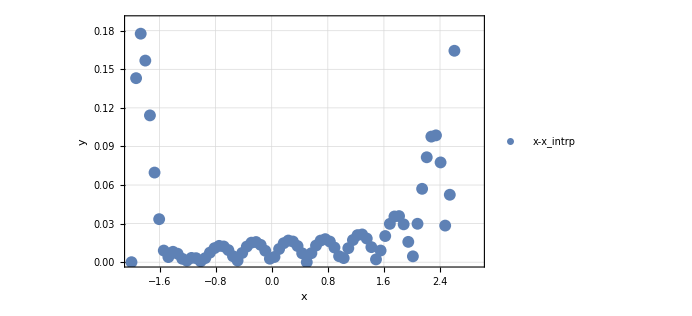

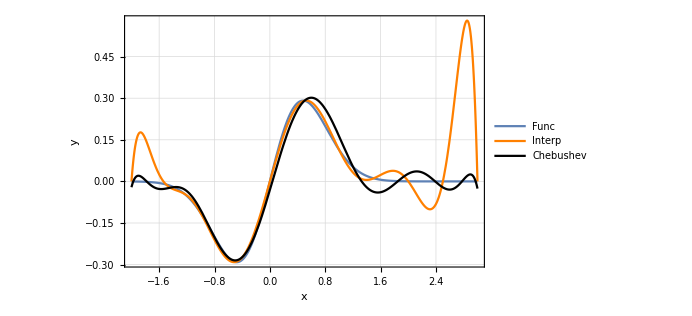

```mathematica
fint[x_]:=InterpolatingPolynomial[{{-2,-0.000305035},{-1.5,-0.0110812},{-1,-0.113881},{-0.5,-0.290786},{0,0},{0.5,0.290786},{1,0.113881},{1.5,0.0110812},{2,0.000305035},{2.5,2.2303*10^-06},{3,2.14925*10^-09}},x];
func[x_]:=Sin[x]*E^(-2*x^2);
data={{-2,1.27055*10^-13},{-1.93421,0.143105},{-1.86842,0.177688},{-1.80263,0.156767},{-1.73684,0.114151},{-1.67105,0.0696922},{-1.60526,0.0334635},{-1.53947,0.00904436},{-1.47368,0.00396682},{-1.40789,0.00808225},{-1.34211,0.00659052},{-1.27632,0.00266334},{-1.21053,0.0011808},{-1.14474,0.00332988},{-1.07895,0.00311513},{-1.01316,0.000691006},{-0.947368,0.00318643},{-0.881579,0.00743272},{-0.815789,0.0109143},{-0.75,0.0126951},{-0.684211,0.0122186},{-0.618421,0.00940605},{-0.552632,0.00466023},{-0.486842,0.00121816},{-0.421053,0.00718519},{-0.355263,0.0121503},{-0.289474,0.0151798},{-0.223684,0.0156717},{-0.157895,0.0134695},{-0.0921053,0.00889646},{-0.0263158,0.00270273},{0.0394737,0.00406457},{0.105263,0.0102445},{0.171053,0.0147656},{0.236842,0.0168336},{0.302632,0.0160687},{0.368421,0.0125716},{0.434211,0.0069053},{0.5,3.7248*10^-14},{0.565789,0.00700244},{0.631579,0.0129362},{0.697368,0.0168},{0.763158,0.0179167},{0.828947,0.0160401},{0.894737,0.011395},{0.960526,0.00464709},{1.02632,0.00319047},{1.09211,0.0108987},{1.15789,0.0172231},{1.22368,0.0210506},{1.28947,0.0215723},{1.35526,0.0184127},{1.42105,0.0117128},{1.48684,0.00215696},{1.55263,0.00906169},{1.61842,0.0203374},{1.68421,0.0298059},{1.75,0.0355498},{1.81579,0.0358452},{1.88158,0.0294338},{1.94737,0.015804},{2.01316,0.00454254},{2.07895,0.0298688},{2.14474,0.0570568},{2.21053,0.0815831},{2.27632,0.0976629},{2.34211,0.0986238},{2.40789,0.0775761},{2.47368,0.0284601},{2.53947,0.0524387},{2.60526,0.164403},{2.67105,0.29951},{2.73684,0.439034},{2.80263,0.548882},{2.86842,0.573904},{2.93421,0.43088}};
Plot1=ListPlot[{data},PlotLegends->Placed[{Style["x-x_intrp",20,Black,FontFamily->"Cambria"]},Right],FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["x",20,Black,FontFamily->"Cambria"],Style["y",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,PlotRange->{Automatic,Automatic}]
Plot3=Plot[fint[x],{x,-2,3},PlotLegends->Placed[{Style["Interp",20,Black,FontFamily->"Cambria"]},Right],PlotStyle->Orange];
Plot31=Plot[{
-0.0309872+
0.844263*x^1+
0.162125*x^2+
-1.23078*x^3+
-0.102802*x^4+
0.66272*x^5+
-0.0147234*x^6+
-0.156917*x^7+
0.0188693*x^8+
0.0137898*x^9+
-0.00279065*x^10
}
,{x,-2,3},PlotLegends->Placed[{Style["Chebushev",20,Black,FontFamily->"Cambria"]},Right],PlotStyle->Black];
Plot2=Plot[func[x],{x,-2,3},PlotLegends->Placed[{Style["Func",20,Black,FontFamily->"Cambria"]},Right]];
Show[{Plot2,Plot3, Plot31},FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["x",20,Black,FontFamily->"Cambria"],Style["y",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,PlotRange->{Automatic,Automatic}]
```

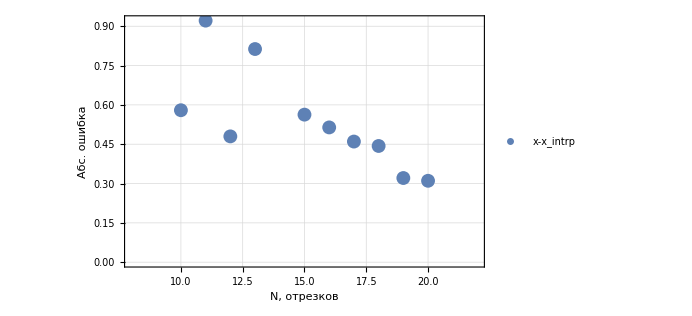

```mathematica
data1={{10,0.579621},{11,0.921377},{12,0.479872},{13,0.813042},{15,0.562793},{16,0.514071},{17,0.460124},{18,0.443268},{19,0.32105},{20,0.310515}};
ListPlot[{data1},PlotLegends->Placed[{Style["x-x_intrp",20,Black,FontFamily->"Cambria"]},Right],FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["N, отрезков",20,Black,FontFamily->"Cambria"],Style["Абс. ошибка",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,PlotRange->{{8,22},Automatic}]
```

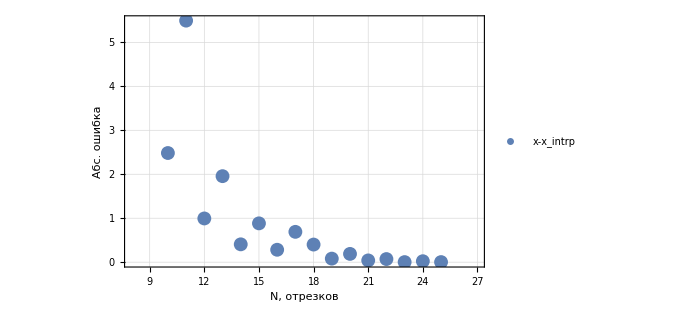

```mathematica
data2={{10,2.48323},{11,5.49473},{12,0.994879},{13,1.95688},{14,0.40618},{15,0.88343},{16,0.282725},{17,0.690232},{18,0.40101},{19,0.0810915},{20,0.1886},{21,0.0403119},{22,0.0711017},{23,0.00220467},{24,0.0222222},{25,0.0024868}};
ListPlot[{data2},PlotLegends->Placed[{Style["x-x_intrp",20,Black,FontFamily->"Cambria"]},Right],FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["N, отрезков",20,Black,FontFamily->"Cambria"],Style["Абс. ошибка",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,PlotRange->{{8,27},Automatic}]
```

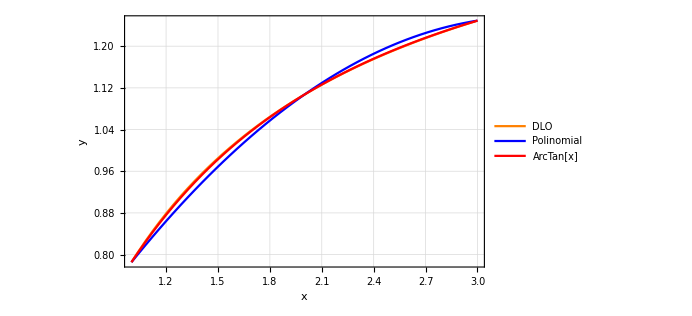

```mathematica
DLO=Plot[{(2.794241*x-0.649834)/(1+x*1.73035)},{x,1,3},PlotLegends->Placed[{Style["DLO",20,Black,FontFamily->"Cambria"]},Right],PlotStyle->Orange];
POL=Plot[{1*0.283794+x*0.591531+x^2*-0.0899267},{x,1,3},PlotLegends->Placed[{Style["Polinomial",20,Black,FontFamily->"Cambria"]},Right],PlotStyle->Blue];
arc=Plot[{ArcTan[x]},{x,1,3},PlotLegends->Placed[{Style["ArcTan[x]",20,Black,FontFamily->"Cambria"]},Right],PlotStyle->Red];
Show[{DLO,POL,arc},FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["x",20,Black,FontFamily->"Cambria"],Style["y",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,PlotRange->{Automatic,Automatic}]
```